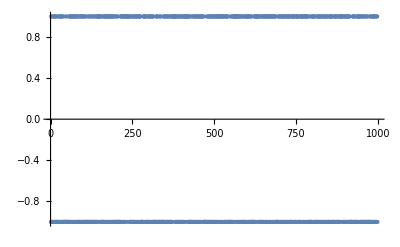

```mathematica
(* we build our own stochastic process *)
(* (a) sequence of independent ups and downs *)
(* (b) sequence of independent, discrete steps up and down *)
(* (c) sequence of independent, normal distributed steps up and down *)
(* (d) sequence of normal distributed steps up and down, variance depending on mean of last two steps *)
NN=1000;
(* do (a) *)
sum1={};
For[j=1,j≤ NN-1,j++,  AppendTo[sum1,2*(RandomInteger[{1,2}]-1.5)]];
ListPlot[sum1]
```

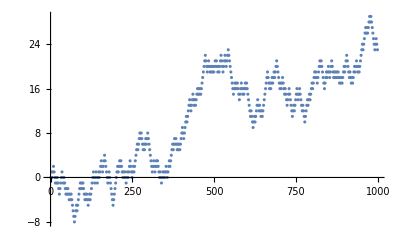

```mathematica
(* do (b) *)
sum1={0};
For[j=1,j≤ NN-1,j++,  AppendTo[sum1,sum1[[j-1]]+2*(RandomInteger[{1,2}]-1.5)]];
ListPlot[sum1]
```

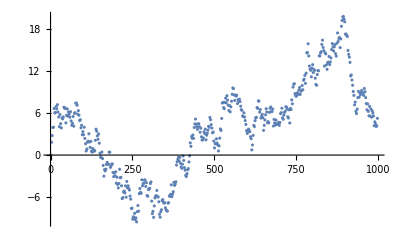

```mathematica
(* do (c) *)
sum1={0};
For[j=1,j≤ NN-1,j++,  AppendTo[sum1,sum1[[j-1]]+RandomVariate[NormalDistribution[0,1.0],1][[1]] ]
];
ListPlot[sum1]
```

1000

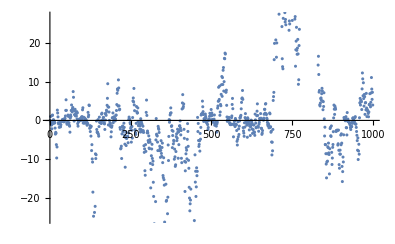

```mathematica
(* do (d) *)
sum1={0,1};
NN=1000
For[j=3,j≤ NN-1,j++,  AppendTo[sum1,sum1[[j-1]]+RandomVariate[NormalDistribution[0,Sqrt[Abs[(sum1[[j-1]]+sum1[[j-2]])]]],1][[1]] ]
];
ListPlot[sum1]
```

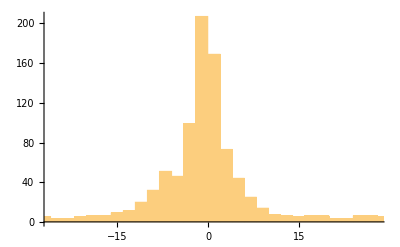

```mathematica
Histogram[sum1]
```

```mathematica
(* check if values are normally distributed *)
(* see: http://reference.wolfram.com/language/ref/DistributionFitTest.html *)
U=DistributionFitTest[sum1,Automatic,"HypothesisTestData"];
U["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 102.295 | 0.
Baringhaus-Henze | 176.325 | 0.
Cramér-von Mises | 21.0155 | 0.
Jarque-Bera ALM | 3074.25 | 0.
Kolmogorov-Smirnov | 0.269979 | 0.
Kuiper | 0.421993 | 0.
Mardia Combined | 3074.25 | 0.
Mardia Kurtosis | 47.4804 | 4.91824827893391×10^-492
Mardia Skewness | 777.368 | 4.49417×10^-171
Pearson χ^2 | 1681.66 | 9.08423035976677×10^-337
Shapiro-Wilk | 0.733261 | 3.37292×10^-37
Watson U^2 | 19.4982 | 0.